Copyright ©, 2015, Erdong Guo and Shu Lin
Author: Erdong Guo and Shu Lin
E-mail: guoerdong@itp.ac.cn, linshu8@mail.sysu.edu.cn
Affliation: Institute of Theoretical Physics, Chinese Academy of Scineces, School of Physics and Astronomy, Sun-Yat Sen University
Description: Calculation tools for AdS/QCD. In the bulk, we turn on the time component of A^{\mu} which introduce finite density in the boundary field theory. Here we show the process how to abstract the quantities in the field theory living in boundary by GKMW relation.

```mathematica
Quit[];
```

```mathematica
H=1+1/#^4&;f=1-1/#^4&;
gtt=-r0^2/2 #^2 f[#]^2/H[#]&;
gxx=r0^2/2 #^2 H[#]&;
gthethe=1;
gphiphi=(ep chi[#])^2&;
gss=1-(ep chi[#])^2&;
grhorho=1/#^2&;
```

```mathematica
$Assumptions=And[chi[rho]>0,chi[rho]<1,k>0];
```

```mathematica
sq1[rho]=Sqrt[-gss[rho]^3(B^2+gxx[rho]^2)(gxx[rho]+k^2gphiphi[rho])/(gtt[rho]grhorho[rho]+(ep At'[rho])^2+gtt[rho]gthethe (ep chi'[rho])^2/gss[rho])];
sq2[rho]=Sqrt[-gss[rho]^3(B^2+gxx[rho]^2)(gtt[rho]grhorho[rho]+(ep At'[rho])^2+gtt[rho]gthethe (ep chi'[rho])^2/gss[rho])/(gxx[rho]gphiphi[rho]k^2)];
sq3[rho]=Sqrt[-gss[rho](B^2+gxx[rho]^2)(gxx[rho]+gphiphi[rho]k^2)(gtt[rho]grhorho[rho]+(ep At'[rho])^2+gtt[rho]gthethe (ep chi'[rho])^2/gss[rho])];
sq4[rho]=Sqrt[-gss[rho]^3(B^2+gxx[rho]^2)(gxx[rho]+gphiphi[rho]k^2)/(gtt[rho]grhorho[rho]+(ep At'[rho])^2+gtt[rho]gthethe (ep chi'[rho])^2/gss[rho])];
```

```mathematica
lieom1=-ep (1+rho^4) (3+(3+4 B^2) rho^4+(5+12 B^2) rho^8+5 rho^12) chi'[rho]-1/rho(-1+rho^4) (1+(2+4 B^2) rho^4+rho^8) ((3 ep (1+rho^4)-2 k^2 rho^2 √(1/(k^2 chi[rho]^2))) √(chi[rho]^2)+ep rho^2 (1+rho^4) chi''[rho])/.{ep->1}//Simplify;
lieom2=(1-2 (5+2 B^2) rho^4-4 (5+8 B^2) rho^8+(-6+4 B^2) rho^12+3 rho^16) At'[rho]+rho (-1+rho^8) (1+(2+4 B^2) rho^4+rho^8) At''[rho]//Simplify;
```

```mathematica
rep={c1->0,c2->1/4 √(c0^2) (-3+√(1/(c0^2 k^2)) k^2),c3->-1/4 √(c0^2) (-3+√(1/(c0^2 k^2)) k^2),c4->1/(64 (1+B^2) √(c0^2))c0 (4 (-1+B^2) c0+3 (1+B^2) √(c0^2) (-1+3 c0^2 √(1/(c0^2 k^2)))-12 (1+3 B^2) c0^3 √(1/(c0^2 k^2))) √(1/(c0^2 k^2)) k^2,a1->0,a3->-a2,a4->(a2 (-3+B^2))/(4 (1+B^2))};
```

```mathematica
eps=1/100;uv=100;
NDSolve[{lieom1==0,lieom2==0,chi[1+eps]== c0+c2 eps^2+c3 eps^3+c4 eps^4,chi'[1+eps]== 2 c2 eps+3 c3 eps^2+4c4 eps^3,At[1+eps]== a0+a2 eps^2+a3 eps^3+a4 eps^4,At'[1+eps]== 2 a2 eps+3 a3 eps^2+4 a4 eps^3}/.rep/.{B->1,c0->1/2,a0->10,a2->2/3,k->1/2},{chi,At},{rho,1+eps,uv}][[1]]
```

{chi→InterpolatingFunction[{{1.01,100.}},<>],At→InterpolatingFunction[{{1.01,100.}},<>]}

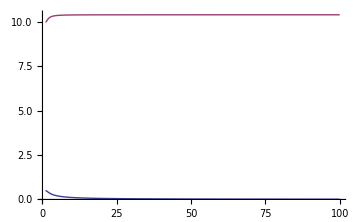

```mathematica
Plot[{chi[rho]/.%,At[rho]/.%},{rho,1+eps,uv}]
```

here we calculate μ with different a0 and find it independent of a0, so we set a0=0 at the horizon.

```mathematica
(At[uv]-At[1+eps])/.%29
```

0.311491

```mathematica
(At[uv]-At[1+eps])/.%32
```

0.311491

```mathematica
(At[uv]-At[1+eps])/.%35
```

0.415321

```mathematica
mum[cc0_,aa2_,kk_,BB_,uv_,eps_]:=
Module[{sol},
sol=NDSolve[{lieom1==0,lieom2==0,chi[1+eps]== c0+c2 eps^2+c3 eps^3+c4 eps^4,chi'[1+eps]== 2 c2 eps+3 c3 eps^2+4c4 eps^3,At[1+eps]== a0+a2 eps^2+a3 eps^3+a4 eps^4,At'[1+eps]== 2 a2 eps+3 a3 eps^2+4 a4 eps^3}/.rep/.{a0->0}/.{c0->cc0,a2->aa2,B->BB,k->kk},{chi,At},{rho,1+eps,uv}][[1]];
{uv chi[uv]/.sol,(At[uv]-At[1+eps])/.sol}]
```

```mathematica
mum[1,1,1,1,100,1/100]
```

{2.33984,0.622982}

Here we tesitify the UV and the IR sensity.

```mathematica
mum[1,1,1,1,150,1/100]
```

{2.34643,0.62306}

```mathematica
mum[1,1,1,1,200,1/100]
```

{2.34973,0.623088}

```mathematica
mum[1,1,1,1,80,1/100]
```

{2.33491,0.622902}

```mathematica
mum[1,1,1,1,50,1/100]
```

{2.32024,0.622558}

```mathematica
mum[1,1,1,1,100,1/80]
```

{2.33984,0.622925}

```mathematica
mum[1,1,1,1,100,1/50]
```

{2.33984,0.622673}

```mathematica
mum[1,1,1,1,100,1/20]
```

{2.33984,0.620412}

```mathematica
dbi=Sqrt[-gss[rho]^3(B^2+gxx[rho]^2)(gxx[rho]+gphiphi[rho]k^2)(grhorho[rho]gtt[rho]+At'[rho]^2+gthethe gtt[rho]chi'[rho]^2/(1-chi[rho])^2)];
wz=k B (1-chi[rho]^2)^2At'[rho];
```

```mathematica
L=dbi+wz//Simplify;
```

```mathematica
repb={chi->Function[rho,rho^(-al)],At->Function[rho,rho^(be)]};
```

```mathematica
Collect[lieom1,{chi''[rho],chi'[rho],chi[rho]}]
```

2 k rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8)-(3 (-1+rho^4) (1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho])/rho+(-1-rho^4) (3+(3+4 B^2) rho^4+(5+12 B^2) rho^8+5 rho^12) chi'[rho]-rho (-1+rho^4) (1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi''[rho]

```mathematica
lieom1=2 k rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8)/(-rho (-1+rho^4) (1+rho^4) (1+(2+4 B^2) rho^4+rho^8) )-(3 (-1+rho^4) (1+rho^4) (1+(2+4 B^2) rho^4+rho^8) chi[rho])/rho/(-rho (-1+rho^4) (1+rho^4) (1+(2+4 B^2) rho^4+rho^8) )+(-1-rho^4) (3+(3+4 B^2) rho^4+(5+12 B^2) rho^8+5 rho^12) /(-rho (-1+rho^4) (1+rho^4) (1+(2+4 B^2) rho^4+rho^8) )chi'[rho]+chi''[rho]//Simplify
```

-(2 k)/(1+rho^4)+(3 chi[rho])/rho^2+((3+(3+4 B^2) rho^4+(5+12 B^2) rho^8+5 rho^12) chi'[rho])/(rho (-1+rho^4) (1+(2+4 B^2) rho^4+rho^8))+chi''[rho]

```mathematica
Series[lieom1/.repb,{rho,Infinity,2}]//Simplify//Normal
```

(3-4 al+al^2) rho^(-2-al)

```mathematica
Coefficient[lieom2,At''[rho]]//Simplify
```

rho (-1+rho^8) (1+(2+4 B^2) rho^4+rho^8)

```mathematica
Collect[lieom2,{At''[rho],At'[rho],At[rho]}]//Simplify
```

(1-2 (5+2 B^2) rho^4-4 (5+8 B^2) rho^8+(-6+4 B^2) rho^12+3 rho^16) At'[rho]+rho (-1+rho^8) (1+(2+4 B^2) rho^4+rho^8) At''[rho]

```mathematica
lieom2=((1-2 (5+2 B^2) rho^4-4 (5+8 B^2) rho^8)/(rho (-1+rho^8) (1+(2+4 B^2) rho^4+rho^8))+(-6+4 B^2) rho^12+3 rho^16)/(rho (-1+rho^8) (1+(2+4 B^2) rho^4+rho^8)) At'[rho]+At''[rho]//Simplify;
```

```mathematica
Series[lieom2/.repb,{rho,Infinity,5}]//Normal//Simplify
```

be rho^(-6+be) (-12-8 B^2+(2+be) rho^4)

```mathematica
repbb={chi->Function[rho,m/rho+c/rho^3],At->Function[rho,a0+a1/rho^2]};
```

```mathematica
Series[lieom2/.repbb,{rho,Infinity,4}]//Simplify
```

O[1/rho]^5

```mathematica
reph={chi->Function[rho,(rho-1)^al],At->Function[rho,(rho-1)^be]};
```

```mathematica
Series[lieom1/.reph,{rho,1,0}]//Simplify//Normal
```

(al^2/(-1+rho)^2+al/(2 (-1+rho))) (-1+rho)^al

```mathematica
Series[L/.repbb/.{ep->1}/.{r0->1},{rho,Infinity,2}]//Simplify
```

rho^3/4-(m^2 rho)/4+m^3/4+(2 B^2+k^2 m^2+m^4)/(4 rho)+(7 c m^2)/(4 rho^2)+O[1/rho]^3